```mathematica
$Version
```

10.4.1 for Linux x86 (64-bit) (April 11, 2016)

Hurst exponent

In the functions: DWT, HurstExponentRS, DFA, and AWC: the second argument is optional; if set to True, it displays also the plot with the fitting. Default is False, and then the output is only a list with two elements: {Hurst exponent, standard error from the fit}

#### DWT (Haar)

```mathematica
DWT[data_,plot_:False]:=Block[{d,n,dwd1,cfs,cfs2,range,P,wav,line,err,linen,slope,hur,label,diagram},
d=data;
n=Floor@Log[2,Length[d]];
dwd1=DiscreteWaveletTransform[d,DaubechiesWavelet[1],n-2,Padding->"Periodic"];
cfs=Reverse[dwd1[{___,1},"Values"]];
cfs2=Table[cfs[[i]]^2,{i,1,Length[cfs]}];
range=Range@Length@cfs2;
P[j_]:=P[j]=Total[cfs2[[j]]]/2^j;
wav=Transpose@{range,Log[2,Table[P[j],{j,range}]]};
line=LinearModelFit[wav,dummy,dummy];
err=line["ParameterErrors"][[2]];
linen=Normal[line];
slope=linen[[2,1]];

Which[-slope>5,"Bias",3<-slope<5,hur=(-slope-3)/2,1<-slope<3,hur=(-slope-1)/2,-1<-slope<1,hur=(-slope+1)/2,slope==0,hur=0.5,-3<-slope<-1,hur=(-slope+3)/2,-slope<-3,"Bias"];
label="H = "<>ToString[hur]<>"+/-"<>ToString[err];
diagram=Show[ListPlot[wav,PlotStyle->{Black,PointSize[Medium]}],Plot[line[dummy],{dummy,First@range-0.1,Last@range+0.1},PlotStyle->Red],Plot[Evaluate@line["MeanPredictionBands",ConfidenceLevel->.99],{dummy,First@range-0.1,Last@range+0.1},PlotStyle->Blue,Filling->{1->{2}}],Frame->True,Axes->False,PlotRange->All,FrameLabel->{"j","log_2(P_j)"},AspectRatio->1,PlotLabel->label];
{hur,err,If[plot==True,diagram,Nothing]}
]
```

#### R/S

This implementation comes from: http://demonstrations.wolfram.com/HurstExponentOfStockPrice/

```mathematica
HurstR[data_] := Module[{zs},
zs = Accumulate[data - Mean[data]];
Max[zs] - Min[zs]
];
HurstS[data_] := StandardDeviation[data];
HurstRS[data_] := If[Abs[HurstS[data]] ≤ 10^-6, 1.0, HurstR[data] / HurstS[data]];
HurstExponentRS[data_,plot_:False] := Module[{n, chunkSize, tmp, helper, model, ndata, label,diagram}, 
n = 2^Round[Log[2, Length[data]]];
ndata = Drop[data,Length[data] - n];
helper = Function[{vs, size}, { Log2[size], Log2[ Mean[Map[HurstRS, Partition[vs, size]]]]}];
chunkSize = NestWhileList[# / 2&, n, # >=4&]//Rest(* dla bin=10 coś się psuje... *);
tmp = Map[helper[ndata, #]&, chunkSize];
tmp = Take[tmp, Length[tmp] - 1];
model =NonlinearModelFit[tmp,A x+B,{A,B},x];
label="H = "<>ToString[Normal[model][[2]]/x]<>"+/-"<>ToString[model["ParameterErrors"][[1]]];
diagram=Show[ListPlot[tmp,Frame->True,Axes->False,PlotStyle->Directive[Black,PointSize[Large]],PlotRange->All,AspectRatio->1],Plot[Normal[model],{x,0,10},Frame->True,PlotStyle->Red],Plot[Evaluate@model["MeanPredictionBands",ConfidenceLevel->.99],{x,0,20},PlotStyle->Directive[Blue,Thickness[0]],Filling->{1->{2}}],FrameLabel->{"Log range size","Log HurstRS ratio"},FrameStyle->Directive[FontSize->13],AspectRatio->1,Axes->False,PlotLabel->label];
{Normal[model][[2]]/x,model["ParameterErrors"][[1]],If[plot==True,diagram,Nothing]}
];
```

#### DFA

```mathematica
DFA[data_,plot_:False]:=Block[{d,Xt,segments,arguments,dfa,nlm,hur,err,label,diagram},
d=data;
Xt=Accumulate[d-Mean[d]]//Chop;
segments=Table[Partition[Xt,2^i,2^i],{i,2,Log2@Length@Xt}];
arguments=Table[Partition[Range@Length@Xt,2^i,2^i],{i,2,Log2@Length@Xt}];
dfa=Log@Table[{2^(i+1),(#[[3]]-Map[#[[1]],#[[2]]])^2&/@Transpose[{NonlinearModelFit[#,a x+b,{a,b},x]&/@(Transpose/@Transpose[{arguments[[i]],segments[[i]]}]),arguments[[i]],segments[[i]]}]//Flatten//Mean//Sqrt},{i,1,Length@segments}];
nlm=NonlinearModelFit[dfa,A t+B,{A,B},t];
hur=Which[0<Normal[nlm][[2]]/t<1,Normal[nlm][[2]]/t,1<Normal[nlm][[2]]/t<2,Normal[nlm][[2]]/t-1];
err=nlm["ParameterErrors"][[1]];
label="H = "<>ToString[Normal[nlm][[2]]/t]<>"+/-"<>ToString[nlm["ParameterErrors"][[1]]];
diagram=Show[ListPlot[dfa,Frame->True,Axes->False,PlotStyle->Black,PlotRange->All,AspectRatio->1],Plot[Normal[nlm],{t,Min@dfa[[All,1]]-0.2,Max@dfa[[All,1]]+0.2},Frame->True,PlotStyle->Red],Plot[Evaluate@nlm["MeanPredictionBands",ConfidenceLevel->.99],{t,Min@dfa[[All,1]]-0.2,Max@dfa[[All,1]]+0.2},PlotStyle->Directive[Blue,Thickness[0]],Filling->{1->{2}}],FrameLabel->{"ln s","ln F(s)"},FrameStyle->Directive[FontSize->13],AspectRatio->1,PlotRange->All,Axes->False,PlotLabel->label];
{hur,err,If[plot==True,diagram,Nothing]}
]
```

#### AWC

```mathematica
AWC[data_,plot_:False]:=Block[{n,cwt,toFitHurst,nlm,slope,hur,err,label,diagram},
n=Floor@Log2[Length[data]];
cwt=ContinuousWaveletTransform[data,GaborWavelet[6],{n,n-1},SampleRate->1];
toFitHurst=Transpose[{cwt["Scales"][[All,2]],Mean/@Abs[cwt[All,"Values"]]}][[8;;]];
nlm=NonlinearModelFit[Log10@toFitHurst,a x+b,{a,b},x];
slope=Normal[nlm][[2]]/x;
{hur,err}={Which[-1.5<slope<-0.5,slope+1.5,-0.5<slope<0.5,slope+0.5,0.5<slope<1.5,slope-0.5,slope>1.5,"Bias"],nlm["ParameterErrors"][[1]]};
label="H = "<>ToString[hur]<>"+/-"<>ToString[err];
diagram=Show[ListPlot[Log10@toFitHurst,Frame->True,Axes->False,AspectRatio->1,PlotRange->All,PlotStyle->Black],Plot[nlm[x],{x,-10,30},PlotStyle->Red],Plot[Evaluate@nlm["MeanPredictionBands",ConfidenceLevel->.99],{x,0,3},PlotStyle->Directive[Blue,Thickness[0]],Filling->{1->{2}}],PlotLabel->label];
{hur,err,If[plot==True,diagram,Nothing]}
]
```

#### fit FARIMA

```mathematica
fitFARIMA[data_]:=Block[{},
(List@@Normal[#])[[2]]&@TimeSeriesModelFit[data,{"FARIMA",{0,0}}]+1/2
]
```

Example: fGn with H=0.75

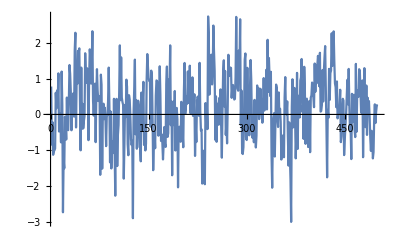

```mathematica
SeedRandom[1]
data=RandomFunction[FractionalGaussianNoiseProcess[0.75],{0,499,1}]["Path"][[All,2]];
ListLinePlot[data]
```

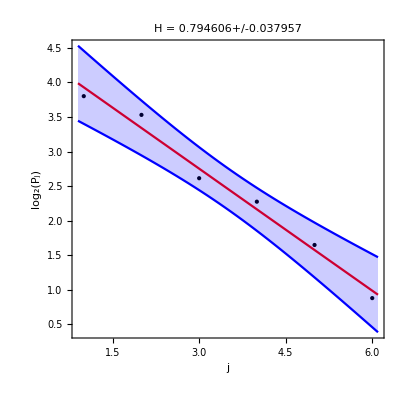
{0.794606,0.037957,-Graphics-}

```mathematica
DWT[data,True]
```

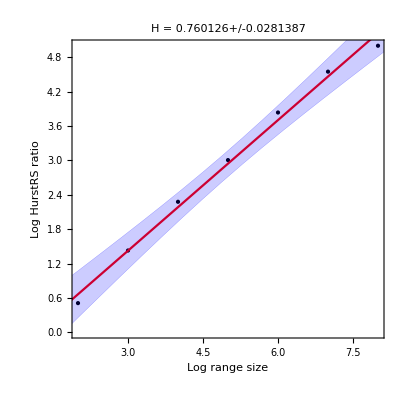
{0.760126,0.0281387,-Graphics-}

```mathematica
HurstExponentRS[data,True]
```

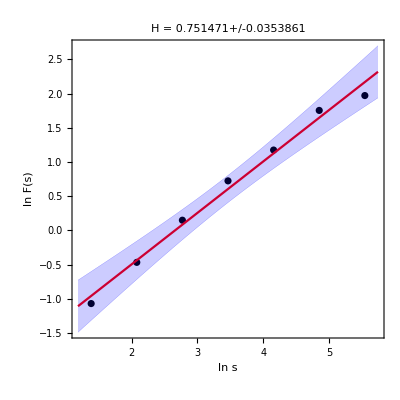
{0.751471,0.0353861,-Graphics-}

```mathematica
DFA[data,True]
```

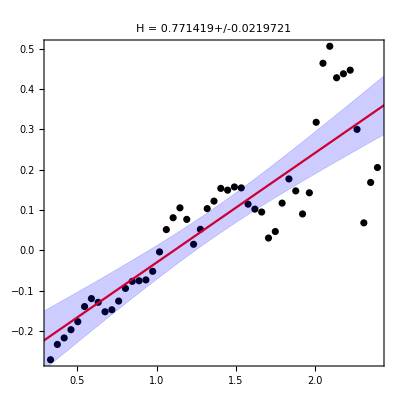
{0.771419,0.0219721,-Graphics-}

```mathematica
AWC[data,True]
```

```mathematica
fitFARIMA[data]
```

0.655675